ReadList::readn: Invalid real number found when reading from grid.txt.

Part::partw: Part 3 of {{-1,-0.5,0,0.5},{$Failed}} does not exist.

Part::partw: Part 4 of {{-1,-0.5,0,0.5},{$Failed}} does not exist.

Riffle::list: List expected at position 1 in Riffle[{{-1,-0.5,0,0.5},{$Failed}}⟦3⟧,{{-1,-0.5,0,0.5},{$Failed}}⟦4⟧].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

Part::partw: Part 3 of {{-1.,-0.5,0,0.5},{$Failed}} does not exist.

Part::partw: Part 4 of {{-1.,-0.5,0,0.5},{$Failed}} does not exist.

Riffle::list: List expected at position 1 in Riffle[{{-1.,-0.5,0,0.5},{$Failed}}⟦3⟧,{{-1.,-0.5,0,0.5},{$Failed}}⟦4⟧].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

Part::partw: Part 3 of {{-1.,-0.5,0.,0.5},{$Failed}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[{{-1.,-0.5,0.,0.5},{$Failed}}⟦3⟧,{{-1.,-0.5,0.,0.5},{$Failed}}⟦4⟧].

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

Riffle::list: List expected at position 1 in Riffle[{{-1.,-0.5,0,0.5},{$Failed}}⟦3⟧,{{-1.,-0.5,0,0.5},{$Failed}}⟦4⟧].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Riffle::argtu will be suppressed during this calculation.

ListLinePlot::lpn: Riffle[Riffle[{{-1.,-0.5,0.,0.5},{$Failed}}⟦3⟧,{{-1.,-0.5,0.,0.5},{$Failed}}⟦4⟧]] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

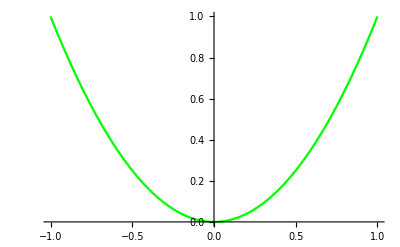
Show[ListLinePlot[Riffle[Riffle[{{-1,-0.5,0,0.5},{$Failed}}⟦3⟧,{{-1,-0.5,0,0.5},{$Failed}}⟦4⟧]],PlotStyle→RGBColor[0, 0, 1]],-Graphics-,PlotRange→All]

-Graphics-

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
list1 = ReadList["uniform.txt", Number, RecordLists->True];
list2 = ReadList["chebysh.txt", Number, RecordLists->True];
uni = Partition[Riffle[list1[[1]], list1[[2]]], 2];
cheb = Partition[Riffle[list2[[1]], list2[[2]]], 2];
```